```mathematica
(*probability of deleterious allele at linked site some time t in the past ND13 eq. 2*)
(*using prob. of recombination b/w focal and linked site = r x, x = Abs[Subscript[s, f]-Subscript[s, L]]*)
(*in general, rx, u, s can be any function of the positions of the focal and linked site*)
(*can also include back mutations, see ND13 supplement*)
pMut:=u/s((r x)/(r x + s)+s/(r x + s)ⅇ^(-r x t - s t));
(*ND13 figure 2*)
Table[pMut/.{u->10^-8,r->4 10^-8,s->10^-2,t->τ,x->Abs[x-5 10^5]},{τ,{0,50,100,150,2 10^2}}];
Plot[%,{x,0,10^6}]
```

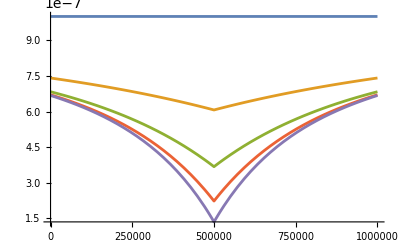

```mathematica
(*ND13 eq. 3*)
(*solving integral that is in the exponent*)
expExpression = - 2 u/s Integrate[(s/(r x + s)(1-Exp[-r x t - s t]))^2,{x,0,l/2},Assumptions->{r>0,s>0,t>0,l>0}]//Collect[#,ⅇ^_]&//Expand
```

(4 ⅇ^(-s t) l u)/(l r+2 s)+(8 ⅇ^(-s t) s u)/(r (l r+2 s))-(8 ⅇ^(-1/2 l r t-s t) s u)/(r (l r+2 s))-(2 l s u)/(l r s+2 s^2)-(2 ⅇ^(-2 s t) l s u)/(l r s+2 s^2)-(4 ⅇ^(-2 s t) s^2 u)/(r (l r s+2 s^2))+(4 ⅇ^(-l r t-2 s t) s^2 u)/(r (l r s+2 s^2))-(4 s t u Gamma[0,s t])/r+(4 s t u Gamma[0,2 s t])/r+(4 s t u Gamma[0,(l r t)/2+s t])/r-(4 s t u Gamma[0,l r t+2 s t])/r

```mathematica
(*confirming our result matches their expression*)
-2 (u l)/(r l)((1-ⅇ^(-s t))^2-s/(s+r l /2)(1-ⅇ^(- s t- r l t / 2))^2+2s t(Gamma[0,s t,2s t]-Gamma[0,r l t /2 + s t,r l t+2 s t]))==%//FullSimplify
```

True

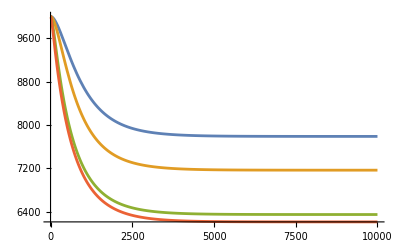

```mathematica
(*approximating the effects of BGS as a time dep. eff. pop size Ne(t)*)
(*ND13 eq. 3*)
(*really a time dependent scaling of the population size given by expExpression*)
(*n here is census size, can be replaced by n(t)*)
ne:=n Exp[expExpression];
(*ND13 fig 3*)
Table[ne/.{u->10^-8,r->4 10^-8,s->10^-3,n->10^4},{l,{5 10^4,10^5,5 10^5,10^6}}];
Plot[%,{t,0,10^4}]
```

```mathematica
(*finding long term equil. Ne*)
```

```mathematica
Limit[ne,t->∞, Assumptions->{l>0,s>0,r>0,u>0,n>0}]
```

ⅇ^(-(2 l u)/(l r+2 s)) n

```mathematica
(*Ne(t) recovers current census size at the present*)
(*but plugging in t=0 is undefined*)
```

```mathematica
Limit[ne,t->0,Assumptions->{l>0,s>0,r>0,u>0,n>0}]
ne/.t->0
```

n

Infinity::indet: Indeterminate expression (0 s u ∞)/r encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Indeterminate

```mathematica
(*result of the t Gamma[0,c t] terms, c = constant*)
(*can probably redifine Times[0,∞] to evaluate to 0 if we care that much*)
{Gamma[0,(l r t)/2+s t]/.t->0,
t Gamma[0,(l r t)/2+s t]/.t->0}
```

Infinity::indet: Indeterminate expression 0 ∞ encountered.

{∞,Indeterminate}

```mathematica
(*in the expressions above time was in generations and backwards in time*)
(*t=0 corresponded to present*)
(*for diffusion we need time to go forward t=0 corresponds to ancestral equil*)
(*and time in genomic units*)
(*need to think about how to automate choosing when to start the diffusion*)
(*how to find when the long term equil is reached*)
```

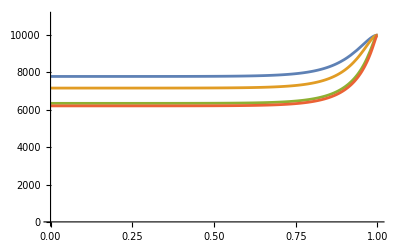

```mathematica
ne=ne/.t-> n t/.t->1-t;
Table[ne/.{u->10^-8,r->4 10^-8,s->10^-3,n->10^4},{l,{5 10^4,10^5,5 10^5,10^6}}];
Plot[%,{t,0,1},PlotRange->{{0,1},{0,11000}}]
```

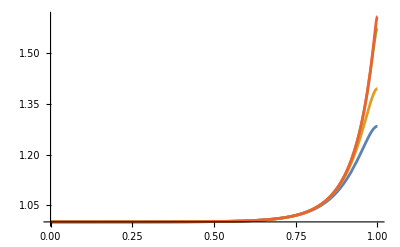

```mathematica
(*for diffusion approx we define v = Ne(t)/Ne(Ancestral)*)
v = ne/(ⅇ^(-(2 l u)/(l r+2 s)) n);
Table[v/.{u->10^-8,r->4 10^-8,s->10^-3,n->10^4},{l,{5 10^4,10^5,5 10^5,10^6}}];
Plot[%,{t,0,1},PlotRange->All]
```

```mathematica
(*ancestral, equilibrium SFS assuming neutrality at focal site*)
equil=θ/x/.θ->4 u (ⅇ^(-(2 l u)/(l r+2 s)) n)
```

(4 ⅇ^(-(2 l u)/(l r+2 s)) n u)/x

```mathematica
(*solving forward in time from this equil using the change of variables from Evansetal07*)
gequil=x(1-x) equil;
nsoln=NDSolve[Evaluate[{D[g[t,x],t]==(x(1-x))/(2 v)D[g[t,x],{x,2}],
g[0,x]==gequil,
g[t,0]==4 ⅇ^(-(2 l u)/(l r+2 s)) n u v (*θ(Ancestral) v*)
}/.{l->10^6,u->10^-8,r->4 10^-8,s->10^-3,n->10^4}],g,{t,0,1-10^-4},{x,0,1},MaxStepSize->0.00025];
```

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

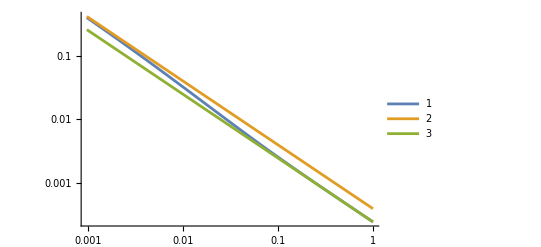

```mathematica
(*plotting against a constant population size*)
LogLogPlot[{g[t,x]/(x(1-x))/.nsoln/.t->1-10^-4,(*time dep BGS apprx.*)
4 n u /x/.{n->10^4,u->10^-8}, (*pop size is census size*)
4 ⅇ^(-(2 l u)/(l r+2 s)) n u/x/.{l->10^6,u->10^-8,r->4 10^-8,s->10^-3,n->10^4} (*pop size is long term limit with BGS*)
},{x,0,1},PlotRange->All,PlotLegends->Automatic]
```

```mathematica
(*subsample the sfs down to a sample of size 10*)
```

```mathematica
Table[NIntegrate[Binomial[10,i] x^i(1-x)^i g[t,x]/(x(1-x))/.nsoln/.t->1-10^-4,{x,0,1}],{i,1,10}]
```

{{0.00128131},{0.000939723},{0.000499088},{0.000186889},{0.0000498037},{9.42899×10^-6},{1.24309×10^-6},{1.08753×10^-7},{5.68579×10^-9},{1.34652×10^-10}}

```mathematica
Table[NIntegrate[Binomial[10,i] x^i(1-x)^i 4 n u /x/.{n->10^4,u->10^-8},{x,0,1}],{i,1,10}]
Table[NIntegrate[Binomial[10,i] x^i(1-x)^i 4 ⅇ^(-(2 l u)/(l r+2 s)) n u/x/.{l->10^6,u->10^-8,r->4 10^-8,s->10^-3,n->10^4} ,{x,0,1}],{i,1,10}]
```

{0.002,0.0015,0.0008,0.0003,0.00008,0.0000151515,1.998×10^-6,1.74825×10^-7,9.14119×10^-9,2.16502×10^-10}

{0.00124229,0.000931718,0.000496916,0.000186344,0.0000496916,9.41129×10^-6,1.24105×10^-6,1.08592×10^-7,5.678×10^-9,1.34479×10^-10}

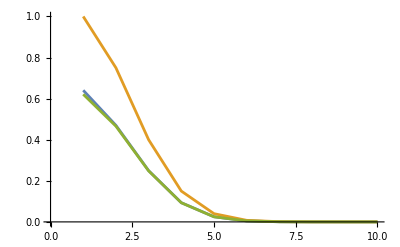

```mathematica
ListLinePlot[{%27//Flatten,%28,%29}/0.002] (*todo whats going on with the scaling?*)
```

```mathematica
(*one region of size l, located l away from the focal site uniform map*)
```

```mathematica
Integrate[u/s(s/(r x + s)(1-ⅇ^(-t(r x +s))))^2,{x,l,2l},Assumptions->{r>0,s>0,t>0,l>0}]
```

1/r s u (ⅇ^(-2 (l r+s) t)/(l r+s)-(2 ⅇ^(-((l r+s) t)))/(l r+s)-ⅇ^(-2 (2 l r+s) t)/(2 l r+s)+(2 ⅇ^(-((2 l r+s) t)))/(2 l r+s)+(l r)/((l r+s) (2 l r+s))+2 t Gamma[0,(l r+s) t]-2 t Gamma[0,2 (l r+s) t]-2 t Gamma[0,(2 l r+s) t]+2 t Gamma[0,2 (2 l r+s) t])

```mathematica
(*replacing the one region with a point mass, distance from focal site to region midpoint is 3/2 l, scaling up mutation rate*)
u/s(s/(r x + s)(1-ⅇ^(-t(r x +s))))^2/.{u -> l u,x->3/2 l}
```

((1-ⅇ^(-(((3 l r)/2+s) t)))^2 l s u)/((3 l r)/2+s)^2

```mathematica
Manipulate[Plot[{Exp[-%]/.{l->regionSize,u->10^-8,r->4 10^-8,s->10^-3,n->10^4},
Exp[-%%]/.{l->regionSize,u->10^-8,r->4 10^-8,s->10^-3,n->10^4}},{t,0,10^4},PlotRange->All,PlotLegends->Automatic],{regionSize,0,10^5}]
```

```mathematica
(*extending to a 1 Mb region with many point masses*)
```

```mathematica
(*ND13 eq. 3*)
(*solving integral that is in the exponent*)
exactExp=- 2 u/s Integrate[(s/(r x + s)(1-Exp[-r x t - s t]))^2,{x,0,l/2},Assumptions->{r>0,s>0,t>0,l>0}];
```

```mathematica
(*approximating as 100 equally spaced point masses*)
Table[i,{i,5 10^3,99.5 10^4,10^4}];
approxExp=Total[Table[-u/s(s/(r x + s)(1-ⅇ^(-t(r x +s))))^2/.{u -> 10^4 u,x->Abs[x-5 10^5]},{x,%14}]];
```

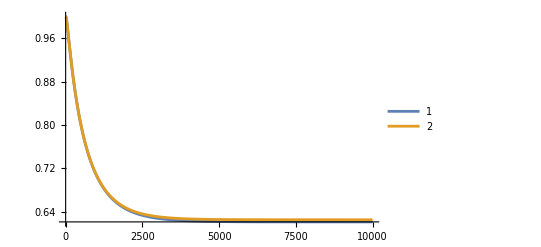

```mathematica
Plot[{Exp[exactExp]/.{l->10^6,u->10^-8,r->4 10^-8,s->10^-3,n->10^4},
Exp[approxExp]/.{u->10^-8,r->4 10^-8,s->10^-3,n->10^4}},{t,0,10^4},PlotRange->All,PlotLegends->Automatic]
```

```mathematica
(*replacing surrounding exon with single pointmass*)
```

```mathematica
(*ND13 eq. 3*)
(*solving integral that is in the exponent*)
exactExp=- 2 u/s Integrate[(s/(r x + s)(1-Exp[-r x t - s t]))^2,{x,0,l/2},Assumptions->{r>0,s>0,t>0,l>0}];
```

```mathematica
(*approximating as 100 equally spaced point masses*)
Table[i,{i,5 10^3,99.5 10^4,10^4}];
approxExp=-u/s(s/(r x + s)(1-ⅇ^(-t(r x +s))))^2/.{u -> 3500 u,x->0};
```

```mathematica
Manipulate[Plot[{Exp[exactExp]/.{l->3500,u->10^-8,s->ss,r->4 10^-8,n->10^4},
Exp[approxExp]/.{u->10^-8,r->4 10^-8,s->ss,n->10^4}},{t,0,tt},PlotRange->All,PlotLegends->Automatic],{ss,10^-8,10^-2},{tt,10^3,10^6}]
```

```mathematica
(*contribution from exon surrounding the focal positions*)
```

```mathematica
Integrate[u/s(s/(r Abs[x-xf] + s)(1-ⅇ^(-t(r Abs[x-xf] +s))))^2,{x,ll,lu},Assumptions->{r>0,s>0,t>0,l>0,ll<xf<lu}]
```

u ((lu-xf)/(lu r+s-r xf)-(ll-xf)/(-ll r+s+r xf)+1/r ⅇ^(-2 s t) (1/(-ll r+s+r xf)ⅇ^(-2 r t xf) (-ⅇ^(2 r t xf) ll r-ⅇ^(2 ll r t) s+ⅇ^(2 r t xf) s+ⅇ^(2 r t xf) r xf+2 ⅇ^(2 t (s+r xf)) s t (-ll r+s+r xf) ExpIntegralEi[-2 s t]-2 ⅇ^(2 t (s+r xf)) s t (-ll r+s+r xf) ExpIntegralEi[2 t (ll r-s-r xf)])+1/(lu r+s-r xf)ⅇ^(-2 lu r t) (ⅇ^(2 lu r t) lu r+ⅇ^(2 lu r t) s-ⅇ^(2 r t xf) s-ⅇ^(2 lu r t) r xf+2 ⅇ^(2 (lu r+s) t) s t (lu r+s-r xf) ExpIntegralEi[-2 s t]-2 ⅇ^(2 (lu r+s) t) s t (lu r+s-r xf) ExpIntegralEi[-2 t (lu r+s-r xf)]))-1/r 2 ⅇ^(-s t) (1/(-ll r+s+r xf)ⅇ^(-r t xf) (-ⅇ^(r t xf) ll r-ⅇ^(ll r t) s+ⅇ^(r t xf) s+ⅇ^(r t xf) r xf+ⅇ^(t (s+r xf)) s t (-ll r+s+r xf) ExpIntegralEi[-s t]-ⅇ^(t (s+r xf)) s t (-ll r+s+r xf) ExpIntegralEi[t (ll r-s-r xf)])+1/(lu r+s-r xf)ⅇ^(-lu r t) (ⅇ^(lu r t) lu r+ⅇ^(lu r t) s-ⅇ^(r t xf) s-ⅇ^(lu r t) r xf+ⅇ^((lu r+s) t) s t (lu r+s-r xf) ExpIntegralEi[-s t]-ⅇ^((lu r+s) t) s t (lu r+s-r xf) ExpIntegralEi[-t (lu r+s-r xf)])))

```mathematica
-Integrate[u/s(s/(r x + s)(1-ⅇ^(-t(r x +s))))^2,{x,0,xf-ll},Assumptions->{r>0,s>0,t>0,l>0,xf>ll}]+-Integrate[u/s(s/(r x + s)(1-ⅇ^(-t(r x +s))))^2,{x,0,lu-xf},Assumptions->{r>0,s>0,t>0,l>0,lu>xf}]
```

-s u ((lu-xf)/(lu r s+s^2-r s xf)-(2 ⅇ^(-s t) (1/s-ⅇ^(r t (-lu+xf))/(lu r+s-r xf)-ⅇ^(s t) t Gamma[0,s t]+ⅇ^(s t) t Gamma[0,t (lu r+s-r xf)]))/r+(ⅇ^(-2 s t) (1/s-ⅇ^(2 r t (-lu+xf))/(lu r+s-r xf)-2 ⅇ^(2 s t) t Gamma[0,2 s t]+2 ⅇ^(2 s t) t Gamma[0,2 t (lu r+s-r xf)]))/r)-u ((-ll+xf)/(-ll r+s+r xf)-(2 ⅇ^(-s t) s (1/s+ⅇ^(r t (ll-xf))/(ll r-s-r xf)-ⅇ^(s t) t Gamma[0,s t]+ⅇ^(s t) t Gamma[0,t (-ll r+s+r xf)]))/r+(ⅇ^(-2 s t) s (1/s+ⅇ^(2 r t (ll-xf))/(ll r-s-r xf)-2 ⅇ^(2 s t) t Gamma[0,2 s t]+2 ⅇ^(2 s t) t Gamma[0,2 t (-ll r+s+r xf)]))/r)

```mathematica
-Integrate[u/s(s/(r x + s)(1-ⅇ^(-t(r x +s))))^2,{x,0,l},Assumptions->{r0>0,r>0,s>0,t>0,l>0}]
```

-s u (l/(l r s+s^2)-(2 ⅇ^(-s t) (1/s-ⅇ^(-l r t)/(l r+s)-ⅇ^(s t) t Gamma[0,s t]+ⅇ^(s t) t Gamma[0,(l r+s) t]))/r+(ⅇ^(-2 s t) (1/s-ⅇ^(-2 l r t)/(l r+s)-2 ⅇ^(2 s t) t Gamma[0,2 s t]+2 ⅇ^(2 s t) t Gamma[0,2 (l r+s) t]))/r)

```mathematica
% //FullSimplify
```

(u ((-l r+ⅇ^(-2 (l r+s) t) s-2 ⅇ^(-((l r+s) t)) s-ⅇ^(-2 s t) (l r+s)+2 ⅇ^(-s t) (l r+s))/(l r+s)-2 s t Gamma[0,s t]+2 s t Gamma[0,2 s t]+2 s t (Gamma[0,(l r+s) t]-Gamma[0,2 (l r+s) t])))/r

```mathematica
%//InputForm
```

(u*((-(l*r) + s/E^(2*(l*r + s)*t) - (2*s)/E^((l*r + s)*t) - (l*r + s)/E^(2*s*t) + (2*(l*r + s))/E^(s*t))/
    (l*r + s) - 2*s*t*Gamma[0, s*t] + 2*s*t*Gamma[0, 2*s*t] + 
   2*s*t*(Gamma[0, (l*r + s)*t] - Gamma[0, 2*(l*r + s)*t])))/r

```mathematica
Limit[%2 ,t->∞,Assumptions->{r0>0,r>0,s>0,l>0}]
```

-(l u)/(l r+s)

```mathematica
Limit[-u/s(s/(r x + s)(1-ⅇ^(-t(r x +s))))^2,t->∞,Assumptions->{r0>0,r>0,s>0,l>0}]
```

ConditionalExpression[-(s u)/(s+r x)^2, u∈ℝ&&s+r x>0]

```mathematica
-Integrate[u/s(s/(r x + s)(1-ⅇ^(-t(r x +s))))^2/.{r x ->r0+r x},{x,lb,ub},Assumptions->{r0>0,r>0,s>0,t>0,ub>lb>0}]
```

-1/r s u (2 t Gamma[0,(lb r+r0+s) t]-2 t Gamma[0,2 (lb r+r0+s) t]+1/((lb r+r0+s) (r0+s+r ub))(-lb r-ⅇ^(-2 t (r0+s+r ub)) (lb r+r0+s)+2 ⅇ^(-t (r0+s+r ub)) (lb r+r0+s)+r ub+ⅇ^(-2 (lb r+r0+s) t) (r0+s+r ub)-2 ⅇ^(-((lb r+r0+s) t)) (r0+s+r ub)-2 (lb r+r0+s) t (r0+s+r ub) Gamma[0,t (r0+s+r ub)]+2 (lb r+r0+s) t (r0+s+r ub) Gamma[0,2 t (r0+s+r ub)]))

```mathematica
%9 //FullSimplify
```

-1/r s u ((-lb r-ⅇ^(-2 t (r0+s+r ub)) (lb r+r0+s)+2 ⅇ^(-t (r0+s+r ub)) (lb r+r0+s)+r ub+ⅇ^(-2 (lb r+r0+s) t) (r0+s+r ub)-2 ⅇ^(-((lb r+r0+s) t)) (r0+s+r ub))/((lb r+r0+s) (r0+s+r ub))+2 t Gamma[0,(lb r+r0+s) t]-2 t Gamma[0,2 (lb r+r0+s) t]+2 t (-Gamma[0,t (r0+s+r ub)]+Gamma[0,2 t (r0+s+r ub)]))

```mathematica
Limit[%11,t->∞,Assumptions->{r0>0,r>0,s>0,ub>lb>0}]
```

(s u (lb-ub))/((lb r+r0+s) (r0+s+r ub))

```mathematica
%3//InputForm
```

-((s*u*((-(lb*r) - (lb*r + r0 + s)/E^(2*t*(r0 + s + r*ub)) + (2*(lb*r + r0 + s))/E^(t*(r0 + s + r*ub)) + 
      r*ub + (r0 + s + r*ub)/E^(2*(lb*r + r0 + s)*t) - (2*(r0 + s + r*ub))/E^((lb*r + r0 + s)*t))/
     ((lb*r + r0 + s)*(r0 + s + r*ub)) + 2*t*Gamma[0, (lb*r + r0 + s)*t] - 
    2*t*Gamma[0, 2*(lb*r + r0 + s)*t] + 2*t*(-Gamma[0, t*(r0 + s + r*ub)] + Gamma[0, 2*t*(r0 + s + r*ub)])))/
  r)

```mathematica
%1 //InputForm
```

-(s*u*(l/(l*r*s + s^2) - (2*(s^(-1) - 1/(E^(l*r*t)*(l*r + s)) - E^(s*t)*t*Gamma[0, s*t] + 
      E^(s*t)*t*Gamma[0, (l*r + s)*t]))/(E^(s*t)*r) + 
   (s^(-1) - 1/(E^(2*l*r*t)*(l*r + s)) - 2*E^(2*s*t)*t*Gamma[0, 2*s*t] + 
     2*E^(2*s*t)*t*Gamma[0, 2*(l*r + s)*t])/(E^(2*s*t)*r)))

```mathematica
%1/.{s->0.03003036016358553, u->1.9854190447839684 10^-8, r->9.862469482192273 10^-10,l->1660.383616387844, t->12410.0}
```

General::munfl: Exp[-745.354] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-751.967] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-752.008] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-0.00109768

```mathematica
%34//InputForm
```

-(s*u*((lu - xf)/(lu*r*s + s^2 - r*s*xf) - (2*(s^(-1) - E^(r*t*(-lu + xf))/(lu*r + s - r*xf) - 
       E^(s*t)*t*Gamma[0, s*t] + E^(s*t)*t*Gamma[0, t*(lu*r + s - r*xf)]))/(E^(s*t)*r) + 
    (s^(-1) - E^(2*r*t*(-lu + xf))/(lu*r + s - r*xf) - 2*E^(2*s*t)*t*Gamma[0, 2*s*t] + 
      2*E^(2*s*t)*t*Gamma[0, 2*t*(lu*r + s - r*xf)])/(E^(2*s*t)*r))) - 
 u*((-ll + xf)/(-(ll*r) + s + r*xf) - (2*s*(s^(-1) + E^(r*t*(ll - xf))/(ll*r - s - r*xf) - 
      E^(s*t)*t*Gamma[0, s*t] + E^(s*t)*t*Gamma[0, t*(-(ll*r) + s + r*xf)]))/(E^(s*t)*r) + 
   (s*(s^(-1) + E^(2*r*t*(ll - xf))/(ll*r - s - r*xf) - 2*E^(2*s*t)*t*Gamma[0, 2*s*t] + 
      2*E^(2*s*t)*t*Gamma[0, 2*t*(-(ll*r) + s + r*xf)]))/(E^(2*s*t)*r))

```mathematica
(*ND13 eq. 3*)
(*solving integral that is in the exponent*)
expExpression = - 2 u/s Integrate[(s/(r x + s)(1-Exp[-r x t - s t]))^2,{x,0,l/2},Assumptions->{r>0,s>0,t>0,l>0}]//Collect[#,ⅇ^_]&//Expand
```

```mathematica
((4 ⅇ^(-s t) l u)/(l r+2 s)+(8 ⅇ^(-s t) s u)/(r (l r+2 s))-(8 ⅇ^(-1/2 l r t-s t) s u)/(r (l r+2 s))-(2 l s u)/(l r s+2 s^2)-(2 ⅇ^(-2 s t) l s u)/(l r s+2 s^2)-(4 ⅇ^(-2 s t) s^2 u)/(r (l r s+2 s^2))+(4 ⅇ^(-l r t-2 s t) s^2 u)/(r (l r s+2 s^2))-(4 s t u Gamma[0,s t])/r+(4 s t u Gamma[0,2 s t])/r+(4 s t u Gamma[0,(l r t)/2+s t])/r-(4 s t u Gamma[0,l r t+2 s t])/r)/2/.l->2l/.l->xf-ll
```

1/2 ((8 ⅇ^(-s t) s u)/(r (2 s+2 r (-ll+xf)))-(8 ⅇ^(-s t-r t (-ll+xf)) s u)/(r (2 s+2 r (-ll+xf)))+(8 ⅇ^(-s t) u (-ll+xf))/(2 s+2 r (-ll+xf))-(4 ⅇ^(-2 s t) s^2 u)/(r (2 s^2+2 r s (-ll+xf)))+(4 ⅇ^(-2 s t-2 r t (-ll+xf)) s^2 u)/(r (2 s^2+2 r s (-ll+xf)))-(4 s u (-ll+xf))/(2 s^2+2 r s (-ll+xf))-(4 ⅇ^(-2 s t) s u (-ll+xf))/(2 s^2+2 r s (-ll+xf))-(4 s t u Gamma[0,s t])/r+(4 s t u Gamma[0,2 s t])/r+(4 s t u Gamma[0,s t+r t (-ll+xf)])/r-(4 s t u Gamma[0,2 s t+2 r t (-ll+xf)])/r)

```mathematica
%32==%31 //FullSimplify
```

True

```mathematica
Integrate[u/s(s/(r x + s)(1-ⅇ^(-t(r x +s))))^2,{x,0,ll-xf},Assumptions->{r>0,s>0,t>0,l>0,xf>ll}]
```

```mathematica
(*one region that is split by a hotspot*)
```

```mathematica
Integrate[u/s(s/(r x +10^-5 Boole[x>2 10^4] + s)(1-ⅇ^(-t(r x +10^-5 Boole[x>2 10^4] +s))))^2,{x,10^4,3 10^4},Assumptions->{r>0,s>0,t>0,l>0}];
```

```mathematica
(*replacing the region with 2 point masses*)
Total[Table[u/s(s/(r x +10^-5 Boole[x>2 10^4] + s)(1-ⅇ^(-t(r x +10^-5 Boole[x>2 10^4] +s))))^2,{x,{1.5 10^4,2.5 10^4}}]]/.u->10^4 u
```

(10000 (1-ⅇ^(-((15000. r+s) t)))^2 s u)/(15000. r+s)^2+(10000 (1-ⅇ^(-((1/100000+25000. r+s) t)))^2 s u)/(1/100000+25000. r+s)^2

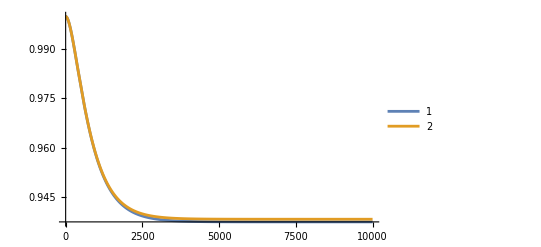

```mathematica
Plot[{Exp[-%37]/.{u->10^-8,r->4 10^-8,s->10^-3,n->10^4},Exp[-%38]/.{u->10^-8,r->4 10^-8,s->10^-3,n->10^4}},{t,0,10^4},PlotRange->All,PlotLegends->Automatic]
```

```mathematica
expExression[Subscript[x, i],Subscript[x, f],t]:=u[Subscript[x, i]]/s[Subscript[x, i]](s[Subscript[x, i]]/(r[Subscript[x, i],Subscript[x, f]]+s[Subscript[x, i]])(1-ⅇ^(-t(r[Subscript[x, i],Subscript[x, f]]+s[Subscript[x, i]]))))^2
```

```mathematica
(*compare with hotspot and without. Does the presence of the hotspot make B(T) look different*)
```

```mathematica
Integrate[u/s(s/(r x +10^-5 Boole[x>2 10^4] + s)(1-ⅇ^(-t(r x +10^-5 Boole[x>2 10^4] +s))))^2,{x,10^4,3 10^4},Assumptions->{r>0,s>0,t>0,l>0}];
```

```mathematica
Integrate[u/s(s/(r x + s)(1-ⅇ^(-t(r x +s))))^2,{x,10^4,3 10^4},Assumptions->{r>0,s>0,t>0,l>0}]
```

s u (ⅇ^(-2 (10000 r+s) t)/(r (10000 r+s))-(2 ⅇ^(-((10000 r+s) t)))/(r (10000 r+s))-ⅇ^(-2 (30000 r+s) t)/(r (30000 r+s))+(2 ⅇ^(-((30000 r+s) t)))/(r (30000 r+s))+20000/((10000 r+s) (30000 r+s))+(2 t Gamma[0,(10000 r+s) t])/r-(2 t Gamma[0,2 (10000 r+s) t])/r-(2 t Gamma[0,(30000 r+s) t])/r+(2 t Gamma[0,2 (30000 r+s) t])/r)

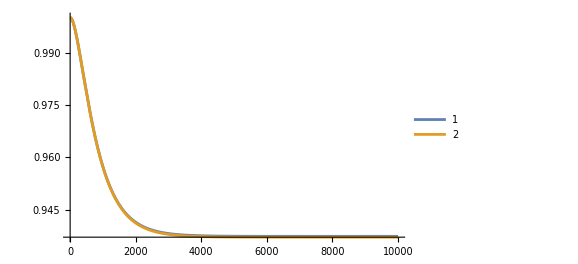

```mathematica
Plot[{Exp[-%31]/.{u->10^-8,r->4 10^-8,s->10^-3,n->10^4},Exp[-%32]/.{u->10^-8,r->4 10^-8,s->10^-3,n->10^4}},{t,0,10^4},PlotRange->All,PlotLegends->Automatic]
```

```mathematica
(* steady state expected SFS eq. 31 in evans *)
equil[S,θ] := θ Exp[2*S+-2*S*(1-x)+Log[1-Exp[2*S*(1-x)]]-(Log[-1*Exp[2*S]+1]+Log[x]+Log[1-x])] 
equil[S,θ]//Simplify
```

((-ⅇ^(2 S)+ⅇ^(2 S x)) θ)/((-1+ⅇ^(2 S)) (-1+x) x)

```mathematica
Integrate[equil[S,θ],{x,0,1}]
```

∫_0^1 (ⅇ^(2 S-2 S (1-x)) (1-ⅇ^(2 S (1-x))) θ)/((1-ⅇ^(2 S)) (1-x) x)ⅆx

```mathematica
eps = 10^-3
Integrate[equil[S,θ],{x,eps,1-eps}]
```

1/1000

(θ (ⅇ^(2 S) (-ExpIntegralEi[-(999 S)/500]+ExpIntegralEi[-S/500])+ExpIntegralEi[S/500]-ExpIntegralEi[(999 S)/500]))/(-1+ⅇ^(2 S))+θ (1+Coth[S]) Log[999]

```mathematica
Integrate[1/x,{x,0,1}]
Integrate[1/x,{x,eps,1-eps}]
```

Integrate::idiv: Integral of 1/x does not converge on {0,1}.

∫_0^1 1/x ⅆx

Log[999]

```mathematica
DSolveValue[D[p[t],t]==-(s+r)p[t]+r u/s,p,t]
```

Function[{t},(ⅇ^(-r t-s t+(r+s) t) r u)/(s (r+s))+ⅇ^(-r t-s t) C[1]]

```mathematica
(ⅇ^(-r t-s t+(r+s) t) r u)/(s (r+s))+ⅇ^(-r t-s t) C[1]//Simplify
```

(r u)/(s (r+s))+ⅇ^(-((r+s) t)) C[1]

```mathematica
DSolveValue[{D[p[t],t]==-(s+r)p[t]+r u/s,p[0]==u/s},p,t]
```

Function[{t},(ⅇ^(-r t-s t) (ⅇ^((r+s) t) r+s) u)/(s (r+s))]

```mathematica
(ⅇ^(-r t-s t) (ⅇ^((r+s) t) r+s) u)/(s (r+s))//Simplify
```

((ⅇ^(-((r+s) t))+r/s) u)/(r+s)

```mathematica
DSolveValue[{D[p[t],t]==-(s+r)p[t]+r u/s,p[0]==p0},p,t]
```

Function[{t},(ⅇ^(-r t-s t) (p0 r s+p0 s^2-r u+ⅇ^((r+s) t) r u))/(s (r+s))]

```mathematica
(ⅇ^(-r t-s t) (p0 r s+p0 s^2-r u+ⅇ^((r+s) t) r u))/(s (r+s))//FullSimplify
```

(ⅇ^(-((r+s) t)) (p0 s (r+s)+(-1+ⅇ^((r+s) t)) r u))/(s (r+s))

```mathematica
%/.p0->u/s
```

(ⅇ^(-((r+s) t)) ((-1+ⅇ^((r+s) t)) r u+(r+s) u))/(s (r+s))

```mathematica
%//Simplify
```

((ⅇ^(-((r+s) t))+r/s) u)/(r+s)

```mathematica
DSolveValue[{D[p[t],t]==-(s+r)p[t]+r u/s,p[0]==equil[S,θ]},p,t]
```

Function[{t},-1/((-1+ⅇ^(2 S)) s (r+s) (-1+x) x)ⅇ^(-r t-s t-2 S (1-x)) (-ⅇ^(2 S+2 S (1-x)) r u x-ⅇ^((r+s) t+2 S (1-x)) r u x+ⅇ^(2 S+(r+s) t+2 S (1-x)) r u x+ⅇ^(2 S (1-x)) r u x+ⅇ^(2 S+2 S (1-x)) r u x^2+ⅇ^((r+s) t+2 S (1-x)) r u x^2-ⅇ^(2 S+(r+s) t+2 S (1-x)) r u x^2-ⅇ^(2 S (1-x)) r u x^2-ⅇ^(2 S) r s θ+ⅇ^(2 S+2 S (1-x)) r s θ-ⅇ^(2 S) s^2 θ+ⅇ^(2 S+2 S (1-x)) s^2 θ)]

```mathematica
-1/((-1+ⅇ^(2 S)) s (r+s) (-1+x) x)ⅇ^(-r t-s t-2 S (1-x)) (-ⅇ^(2 S+2 S (1-x)) r u x-ⅇ^((r+s) t+2 S (1-x)) r u x+ⅇ^(2 S+(r+s) t+2 S (1-x)) r u x+ⅇ^(2 S (1-x)) r u x+ⅇ^(2 S+2 S (1-x)) r u x^2+ⅇ^((r+s) t+2 S (1-x)) r u x^2-ⅇ^(2 S+(r+s) t+2 S (1-x)) r u x^2-ⅇ^(2 S (1-x)) r u x^2-ⅇ^(2 S) r s θ+ⅇ^(2 S+2 S (1-x)) r s θ-ⅇ^(2 S) s^2 θ+ⅇ^(2 S+2 S (1-x)) s^2 θ)//Simplify
```

(ⅇ^(-((r+s) t)) ((-1+ⅇ^(2 S)) (-1+ⅇ^((r+s) t)) r u (-1+x) x+(-ⅇ^(2 S)+ⅇ^(2 S x)) r s θ-(ⅇ^(2 S)-ⅇ^(2 S x)) s^2 θ))/((-1+ⅇ^(2 S)) s (r+s) (-1+x) x)

```mathematica
u n (1-p)/(n p)
```

((1-p) u)/p

```mathematica
%//FullSimplify
```

(-1+1/p) u

```mathematica
%%/.p->u/s
```

(-1+s/u) u

```mathematica
%//FullSimplify
```

s-u

```mathematica
u n (1-p)/(n p)/.p->u/s
```

s (1-u/s)